This file is to generate the figures in the supplementary section 5.

```mathematica
saveDir=NotebookDirectory[]
```

C:\Dropbox\Input_output_theory\Laser_theory\Clean_codes_for_paper\testing\

```mathematica
ϕ0 = Quantity["ReducedPlanckConstant"]/(2Quantity["ElementaryCharge"])
```

1/2 ℏ/e

```mathematica
combineOps[op1_,op2_]:=Module[{top},
top = TensorProduct[op1,op2];
top = Flatten[Transpose[top,{1,3,4,2}],1];
top = Flatten[Transpose[top,{3,1,2}],1];
Return[topᵀ]
]
```

This file is generated by Main_Manuscript_figures.nb

```mathematica
Get[FileNameJoin[{saveDir,"ABOCC_m0_vs_Zc_data.m"}]];
```

```mathematica
fit=LinearModelFit[{(#[[1]])^-1,#[[2]]}&/@posTb,x,x]
```

FittedModel[0.514286+6356.43 x]

```mathematica
generateAops[phic_,bigPhi_,rac_,nMax_?IntegerQ,m0_?IntegerQ]:=Module[{Aop1,Aop2},
Quiet[Aop1 = bigPhi Exp[-phic^2/2](1.0 phic aop+Sum[(-1.0)^j phic^(2j+1)/(Factorial[j] Factorial[j+1])MatrixPower[aopᵀ,j].MatrixPower[aop,j+1],{j,1,nMax}])];
Aop2 =2 rac phic aop;

Aopc=Aop1+Aop2;
Aopc=Aopc/(Diagonal[Aopc,1][[m0]]);
]
```

```mathematica
updateABOCCopsNew[zc_?NumericQ]:=Module[{},
m0=Round[fit[1/zc]];
maxN = Round[2.5 m0];


aTrunc =Floor[maxN];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],
SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};

phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))];
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

generateAops[phic,bigPhi,0.418,maxN,m0];
AopcD=Aopcᵀ;

AOpc= KroneckerProduct[Aopc,SparseArray[IdentityMatrix[2]]];
AOpcD=KroneckerProduct[AopcD,SparseArray[IdentityMatrix[2]]];
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( projectorD.combineOps[hac,iOp].projector-projectorD.combineOps[iOp,hac].projector);
pumpSO = -1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2projectorD.combineOps[sP,sM].projector);
normalLossSO = -1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2 projectorD.combineOps[aOp,aOpᵀ].projector);
lossSO = -1/2(projectorD.combineOps[AOpcᵀ.AOpc,iOp].projector+projectorD.combineOps[iOp,AOpcᵀ.AOpc].projector-2 projectorD.combineOps[AOpc,AOpcᵀ].projector);
Speak["Operators are updated."]
]
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
tempFun2[lambda_?NumericQ,gr_?NumericQ]:=Module[{γ,g},

γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{nAvg,rate}]
]
```

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third,fourth,fifth},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[dim-3],Range[4,dim]}],Transpose[{Range[4,dim],Range[dim-3]}]];

fourth = Join[Transpose[{Range[dim-4],Range[5,dim]}],Transpose[{Range[5,dim],Range[dim-4]}]];

fifth = Join[Transpose[{Range[1,dim-5,2],Range[6,dim,2]}], Transpose[{Range[6,dim,2],Range[1,dim-5,2]}]];

Return[Join[center,first,second,third,fourth,fifth]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

```mathematica
tempfun3[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[{nAvg,rate,Log[Abs[ev[[-2]]]],steady}]
]
```

```mathematica
Get[FileNameJoin[{saveDir,"ABOCC_SO_m0_"<>ToString[1000]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];
```

```mathematica
zcList=Table[{m0Target,1/x/.Solve[fit[x]==m0Target,x][[1]]},{m0Target,100,1600,100}]
```

{{100,63.8929},{200,31.8641},{300,21.2245},{400,15.9115},{500,12.7259},{600,10.6031},{700,9.08729},{800,7.95065},{900,7.06674},{1000,6.3597},{1100,5.78127},{1200,5.29929},{1300,4.8915},{1400,4.54197},{1500,4.23907},{1600,3.97405}}

```mathematica
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
res1
```

{-20.2698,{x→3.5,y→1.0013}}

```mathematica
gBest = y x/2 √(1.0/(x- 2))/.res1[[2]]
```

1.43072

```mathematica
tempfun3[x/.res1[[2]],gBest]
```

{1079.03+1.70918×10^-8 ⅈ,1.00195+6.36961×10^-13 ⅈ,-20.2698,SparseArray[…]}

```mathematica
lambdaCrude= Range[2.5,5.5,0.05];
lambdaFine1 = Range[3.45,3.55,0.01];
lambdaFine2 = Range[4.65,4.75,0.01];
lambdaCoord = Union[lambdaCrude,lambdaFine1,lambdaFine2];
Length[lambdaCoord]
```

77

```mathematica
Monitor[
lambdaSweep = Table[
resTemp = tempfun3[lambdaCoord[[j]],gBest];
Flatten[{lambdaCoord[[j]],resTemp},1]
,{j,Length[lambdaCoord]}];
,j]
```

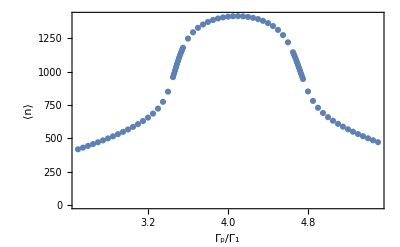

```mathematica
ListPlot[Re[lambdaSweep[[All,{1,2}]]]
,Frame->True
,FrameLabel->{"Γ_p/Γ_1","⟨n⟩"}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]]
```

```mathematica
projCavityg = KroneckerProduct[IdentityMatrix[Length[aop],SparseArray],{1,0}];
projCavityg//Dimensions
```

{2501,5002}

```mathematica
projCavitye = KroneckerProduct[IdentityMatrix[Length[aop],SparseArray],{0,1}];
projCavitye//Dimensions
```

{2501,5002}

```mathematica
partialTraceAtom[mtx_]:=Module[{},
Return[projCavityg.mtx.projCavitygᵀ+projCavitye.mtx.projCavityeᵀ]
]
```

```mathematica
Monitor[
lambdaSweepDist = Table[
Chop[Diagonal[partialTraceAtom[lambdaSweep[[j,-1]]]]]
,{j,Length[lambdaSweep]}];
,j]
```

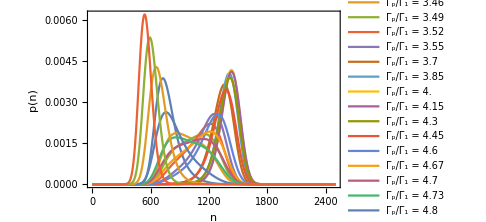

```mathematica
ListPlot[lambdaSweepDist[[18;;-5;;3]]
,ImageSize->5 72
,FrameLabel->{"n","p(n)"}
,Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->Full
,PlotLegends->(Style["Γ_p/Γ_1 = "<>ToString[#],Black,FontFamily->"Cambria"]&/@lambdaSweep[[18;;-5;;3,1]])
,Joined->True]
```

```mathematica
linewidthPlot= {#[[1]],Chop[Exp[#[[4]]]/(Tr[AOpc.#[[5]].AOpcD]/(4 Abs[#[[2]]]^2))]}&/@lambdaSweep;
```

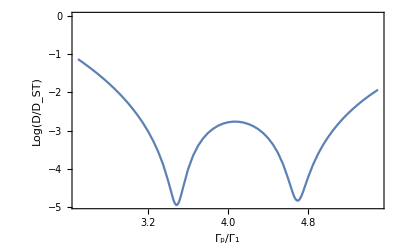

```mathematica
ListPlot[{#[[1]],Log[#[[2]]]}&/@linewidthPlot
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_p/Γ_1","Log(D/D_ST)"}
(*,PlotRange->{-12.5,-7}*)
,Joined->True
]
```

```mathematica
lambdaBest = x/.res1[[2]]
```

3.5

```mathematica
gSweepCrude = Range[0.9,1.1,0.005] gBest;
gSweepFine = Range[0.99,1.01,0.001]gBest;
gSweepCoord = Union[gSweepCrude,gSweepFine]
```

{1.28765,1.2948,1.30196,1.30911,1.31626,1.32342,1.33057,1.33772,1.34488,1.35203,1.35918,1.36634,1.37349,1.38065,1.3878,1.39495,1.40211,1.40926,1.41641,1.41784,1.41928,1.42071,1.42214,1.42357,1.425,1.42643,1.42786,1.42929,1.43072,1.43215,1.43358,1.43501,1.43644,1.43787,1.43787,1.43931,1.44074,1.44217,1.4436,1.44503,1.45218,1.45934,1.46649,1.47364,1.4808,1.48795,1.4951,1.50226,1.50941,1.51656,1.52372,1.53087,1.53803,1.54518,1.55233,1.55949,1.56664,1.57379}

```mathematica
Monitor[
gSweep = Table[
resTemp = tempfun3[lambdaBest,gSweepCoord[[j]]];
Flatten[{gSweepCoord[[j]],resTemp},1]
,{j,Length[gSweepCoord]}];
,j]
```

```mathematica
Monitor[
gSweepDist = Table[
Chop[Diagonal[partialTraceAtom[gSweep[[j,-1]]]]]
,{j,Length[gSweep]}];
,j]
```

```mathematica
linewidthPlot2= {#[[1]],Chop[Exp[#[[4]]]/(Tr[AOpc.#[[5]].AOpcD]/(4 Abs[#[[2]]]^2))]}&/@gSweep;
```

```mathematica
rescaleFun2[x_]:=(5/(2000-200))(x-2000)
```

#### Sweep g/g1 = 1.0

```mathematica
rescaleFun[x_]:=(5/(1400-200))(x-1400)
```

```mathematica
rescaleFun[1400]
```

0

```mathematica
lambdaBest = x/.res1[[2]]
```

3.5

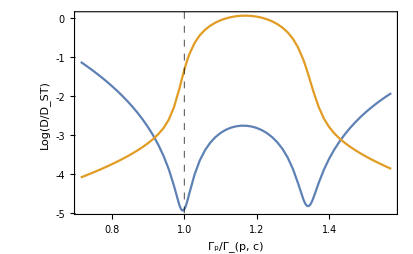

```mathematica
ListPlot[{{#[[1]]/lambdaBest,Log[#[[2]]]}&/@linewidthPlot,{#[[1]]/lambdaBest,rescaleFun[Re[#[[2]]]]}&/@lambdaSweep}
,Frame->True
,Joined->True
,ImageSize->5.75 72
,FrameLabel->{{"Log(D/D_ST)",Rotate["⟨n⟩",π]},{"Γ_p/Γ_(p, c)",None}}
,GridLines->{{{1,Directive[Black,Dashed,Opacity[1]]}},None}
,FrameTicks->{{{-5,-4,-3,-2,-1,0},{{rescaleFun[1400],1400},{rescaleFun[1000],1000},{rescaleFun[600],600},{rescaleFun[200],200}}},Automatic}
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Cambria"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Cambria"]},{Directive[Black,FontSize->16,FontFamily->"Cambria"],Directive[Black,FontSize->16,FontFamily->"Cambria"]}}]
```

```mathematica
Monitor[
lambdaSweepRedo =Table[
resTemp = tempfun3[ratio lambdaBest,gBest];
Flatten[{ratio lambdaBest,resTemp},1]
,{ratio,0.95,1.05,0.025}];
,ratio]
lambdaSweepRedoDist =  Table[
Chop[Diagonal[partialTraceAtom[lambdaSweepRedo[[j,-1]]]]]
,{j,Length[lambdaSweepRedo]}];
```

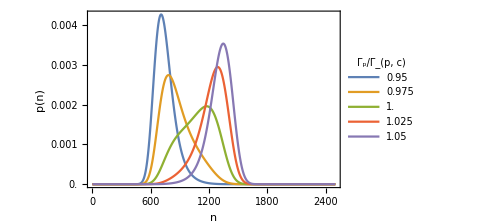

```mathematica
g1distPlot=ListPlot[lambdaSweepRedoDist
,ImageSize->5 72
,FrameLabel->{"n","p(n)"}
,Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->Full
,FrameTicks->{{{0.0,0.001,0.002,0.003,0.004},None},{Automatic,Automatic}}
(*,PlotLegends->(Style["Γ_p/Γ_1 = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@lambdaSweep[[posList,1]])*)
,PlotLegends->Placed[
LineLegend[lambdaSweepRedo[[All,1]]/lambdaBest,LegendLabel->"Γ_p/Γ_(p, c)",LabelStyle->Directive[Black,14,FontFamily->"Cambria"],LegendFunction->(Framed[#1,RoundingRadius->5,FrameStyle->Directive[Black,Thin]]&)]
,{0.85,0.5}]
,Joined->True]
```

```mathematica
tempfun2[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
gSweepCoord1 = Select[gSweepCoord,#/gBest<0.99&]
Monitor[
bestLambdaList1 = Table[
resTemp = FindMinimum[Re[tempfun2[x,gSweepCoord1[[j]]]],{x,2.7,4.0}(*,PrecisionGoal->5,AccuracyGoal->5*)];
x/.resTemp[[2]]
,{j,Length[gSweepCoord1]}];
,j]
```

{1.28765,1.2948,1.30196,1.30911,1.31626,1.32342,1.33057,1.33772,1.34488,1.35203,1.35918,1.36634,1.37349,1.38065,1.3878,1.39495,1.40211,1.40926}

```mathematica
bestLambdaList1
```

{3.43614,3.46784,3.49958,3.53134,3.56313,3.59494,3.62677,3.65861,3.69045,3.7223,3.75415,3.78597,3.81778,3.84957,3.88132,3.91305,3.94477,3.97603}

```mathematica
gSweepCoord2 = Select[gSweepCoord,#/gBest≥0.99&]
Monitor[
bestLambdaList2 = Table[
resTemp = FindMinimum[Re[tempfun2[x,gSweepCoord2[[j]]]],{x,2.7,4.0}(*,PrecisionGoal->5,AccuracyGoal->5*)];
x/.resTemp[[2]]
,{j,Length[gSweepCoord2]}];
,j]
```

{1.41641,1.41784,1.41928,1.42071,1.42214,1.42357,1.425,1.42643,1.42786,1.42929,1.43072,1.43215,1.43358,1.43501,1.43644,1.43787,1.43787,1.43931,1.44074,1.44217,1.4436,1.44503,1.45218,1.45934,1.46649,1.47364,1.4808,1.48795,1.4951,1.50226,1.50941,1.51656,1.52372,1.53087,1.53803,1.54518,1.55233,1.55949,1.56664,1.57379}

```mathematica
bestLambdaList2
```

{3.88227,3.79785,3.7412,3.69641,3.65864,3.6256,3.59604,3.56917,3.54448,3.52155,3.50013,3.47999,3.46098,3.44295,3.42579,3.40941,3.40941,3.39374,3.3787,3.36426,3.35034,3.33692,3.27606,3.22341,3.17691,3.13524,3.09747,3.06292,3.03111,3.00162,2.97416,2.94848,2.92437,2.90166,2.8802,2.85988,2.84058,2.82223,2.80474,2.78803}

```mathematica
gSweepCoord3=Range[0.986,0.989,0.001]gBest;
Monitor[
bestLambdaList3 = Table[
resTemp = FindMinimum[Re[tempfun2[x,gSweepCoord3[[j]]]],{x,3.6,4.2}(*,PrecisionGoal->5,AccuracyGoal->5*)];
x/.resTemp[[2]]
,{j,Length[gSweepCoord3]}];
,j]
```

```mathematica
bestLambdaList3
```

{3.98188,3.9873,3.99168,3.99019}

```mathematica
bestLambdaList2[[Position[gSweepCoord2/gBest,1.05][[1,1]]]]
```

3.00162

```mathematica
allCoord =Join[Transpose[{gSweepCoord1,bestLambdaList1}]
,Transpose[{gSweepCoord3,bestLambdaList3}]
,Transpose[{gSweepCoord2,bestLambdaList2}]];
Print["allCoord Length = ",Length[allCoord]]
Monitor[
bestSweepRes = Table[
Flatten[{allCoord[[j]],tempfun3[allCoord[[j,2]],allCoord[[j,1]]]},1]
,{j,Length[allCoord]}];
,j]
```

allCoord Length = 62

```mathematica
rescaleFun3[x_]:=(5/(1100-300))(x-1100)
```

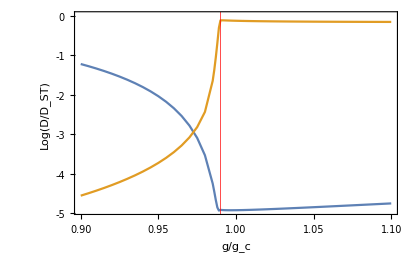

```mathematica
bestPlot = ListPlot[{{(#[[1]])/gBest,Log[Exp[#[[5]]]/Abs[(#[[4]])/(4 (#[[3]])^2)]]}&/@bestSweepRes,{#[[1]]/gBest,rescaleFun3[Re[#[[3]]]]}&/@bestSweepRes}
,Frame->True
,Joined->True
,ImageSize->5.75 72
,FrameLabel->{{"Log(D/D_ST)",Rotate["⟨n⟩",π]},{"g/g_c",None}}
,GridLines->{{{0.99,Directive[Red,Opacity[1]]}},None}
,FrameTicks->{{{-5,-4,-3,-2,-1,0},{{rescaleFun3[1000],1000},{rescaleFun3[800],800},{rescaleFun3[600],600},{rescaleFun3[400],400}}},Automatic}
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Cambria"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Cambria"]},{Directive[Black,FontSize->16,FontFamily->"Cambria"],Directive[Black,FontSize->16,FontFamily->"Cambria"]}}]
```

```mathematica
temp[x_?NumericQ]:=Module[{t},
t=(tempfun3[x,1.05 gBest]);
Return[Chop[Exp[#[[3]]]/(Tr[AOpc.#[[4]].AOpcD]/(4 Abs[#[[1]]]^2))]&@t]
]
```

```mathematica
lambdaBest1p05=x/.(FindMinimum[temp[x],{x,2.9,3.1}])[[2]]
```

2.99602

```mathematica
Monitor[
lambdaSweep1p05 = Table[
resTemp = tempfun3[ratio lambdaBest1p05,1.05gBest];
Flatten[{ratio lambdaBest1p05,resTemp},1]
,{ratio,0.7,2.5,0.05}];
,ratio]
```

```mathematica
linewidthPlot1p05= {#[[1]],Chop[Exp[#[[4]]]/(Tr[AOpc.#[[5]].AOpcD]/(4 Abs[#[[2]]]^2))]}&/@lambdaSweep1p05;
```

```mathematica
g1p05CoordCrude = Range[0.7,1.3,0.025]lambdaBest1p05;
g1p05CoordFine = Range[0.85,1.15,0.005] lambdaBest1p05;
g1p05CoordFine2 = Range[0.99,1.01,0.001] lambdaBest1p05;
g1p05Coord=Union[g1p05CoordCrude,g1p05CoordFine,g1p05CoordFine2];
Length[g1p05Coord]
```

90

```mathematica
Monitor[
lambdaSweep1p05 = Table[
resTemp = tempfun3[g1p05Coord[[j]],1.05gBest];
Flatten[{g1p05Coord[[j]],resTemp},1]
,{j,Length[g1p05Coord]}];
,j]
```

```mathematica
linewidthPlot1p05= {#[[1]],Chop[Exp[#[[4]]]/(Tr[AOpc.#[[5]].AOpcD]/(4 Abs[#[[2]]]^2))]}&/@lambdaSweep1p05;
```

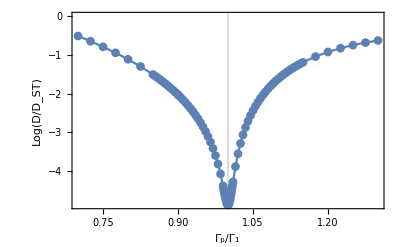

```mathematica
ListPlot[{#[[1]]/lambdaBest1p05,Log[#[[2]]]}&/@linewidthPlot1p05
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_p/Γ_1","Log(D/D_ST)"}
(*,PlotRange->{-12.5,-7}*)
,Joined->True
,GridLines->{{{1.0,Directive[Black,FontSize->16,FontFamily->"Cambria"]}},None}
,PlotMarkers->Automatic
]
```

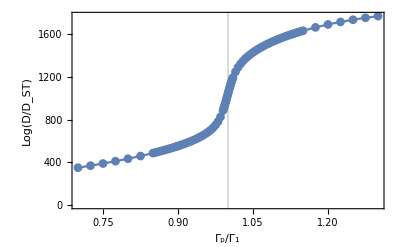

```mathematica
ListPlot[{#[[1]]/lambdaBest1p05,Abs[#[[2]]]}&/@lambdaSweep1p05
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_p/Γ_1","Log(D/D_ST)"}
(*,PlotRange->{-12.5,-7}*)
,Joined->True
,GridLines->{{{1.0,Directive[Black,FontSize->16,FontFamily->"Cambria"]}},None}
,PlotMarkers->Automatic
]
```

```mathematica
rescaleFun1p05[x_]:=(5/(1800-100))(x-1800)
```

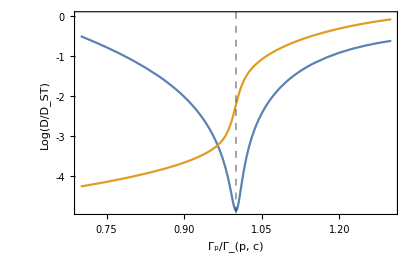

```mathematica
sweep1p05Plot = ListPlot[{{#[[1]]/lambdaBest1p05,Log[#[[2]]]}&/@linewidthPlot1p05,{#[[1]]/lambdaBest1p05,rescaleFun1p05[Re[#[[2]]]]}&/@lambdaSweep1p05}
,Frame->True
,Joined->True
,ImageSize->5.75 72
,FrameLabel->{{"Log(D/D_ST)",Rotate["⟨n⟩",π]},{"Γ_p/Γ_(p, c)",None}}
,GridLines->{{{1.0,Directive[Black,Dashed,Opacity[1]]}},None}
,FrameTicks->{{{-5,-4,-3,-2,-1,0},{{rescaleFun1p05[1600],1600},{rescaleFun1p05[1200],1200},{rescaleFun1p05[800],800},{rescaleFun1p05[400],400}}},Automatic}
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Cambria"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Cambria"]},{Directive[Black,FontSize->16,FontFamily->"Cambria"],Directive[Black,FontSize->16,FontFamily->"Cambria"]}}
]
```

```mathematica
Monitor[
lambdaSweep1p05Dist = Table[
Chop[Diagonal[partialTraceAtom[lambdaSweep1p05[[j,-1]]]]]
,{j,Length[lambdaSweep1p05]}];
,j]
```

```mathematica
Monitor[
lambdaSweep1p05Redo =Table[
resTemp = tempfun3[ratio  lambdaBest1p05,1.05gBest];
Flatten[{ratio lambdaBest1p05,resTemp},1]
,{ratio,0.95,1.05,0.025}];
,ratio]
lambdaSweep1p05RedoDist =  Table[
Chop[Diagonal[partialTraceAtom[lambdaSweep1p05Redo[[j,-1]]]]]
,{j,Length[lambdaSweep1p05Redo]}];
```

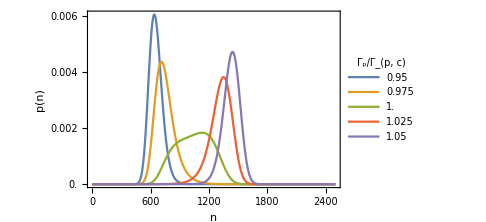

```mathematica
g1dist1p05Plot=ListPlot[lambdaSweep1p05RedoDist
,ImageSize->5 72
,FrameLabel->{"n","p(n)"}
,Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->Full
,FrameTicks->{{{0.0,0.002,0.004,0.006},None},{Automatic,Automatic}}
(*,PlotLegends->(Style["Γ_p/Γ_1 = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@lambdaSweep[[posList,1]])*)
,PlotLegends->Placed[
LineLegend[lambdaSweepRedo[[All,1]]/lambdaBest,LegendLabel->"Γ_p/Γ_(p, c)",LabelStyle->Directive[Black,14,FontFamily->"Cambria"],LegendFunction->(Framed[#1,RoundingRadius->5,FrameStyle->Directive[Black,Thin]]&)]
,{0.85,0.5}]
,Joined->True]
```

```mathematica
bestLambdaList1[[Position[gSweepCoord1/gBest,n_ /; n==0.95][[1,1]]]]
```

3.75415

```mathematica
temp[x_?NumericQ]:=Module[{t},
t=(tempfun3[x,0.95 gBest]);
Return[Chop[Exp[#[[3]]]/(Tr[AOpc.#[[4]].AOpcD]/(4 Abs[#[[1]]]^2))]&@t]
]
```

```mathematica
lambdaBest0p95=x/.(FindMinimum[temp[x],{x,3.6,3.8}])[[2]]
```

3.77919

```mathematica
g0p95CoordCrude = Range[0.5,1.5,0.025]lambdaBest0p95;
g0p95CoordFine = Range[0.9,1.1,0.005] lambdaBest0p95;
(*g1p05CoordFine2 = Range[0.99,1.01,0.001] lambdaBest0p95;*)
g0p95Coord=Union[g0p95CoordCrude,g0p95CoordFine(*,g1p05CoordFine2*)];
Length[g0p95Coord]
```

76

```mathematica
Monitor[
lambdaSweep0p95 = Table[
resTemp = tempfun3[g0p95Coord[[j]],0.95gBest];
Flatten[{g0p95Coord[[j]],resTemp},1]
,{j,Length[g0p95Coord]}];
,j]
```

```mathematica
rescaleFun0p95[x_]:=(2/(600-200))(x-600)
```

```mathematica
linewidthPlot0p95= {#[[1]],Chop[Exp[#[[4]]]/(Tr[AOpc.#[[5]].AOpcD]/(4 Abs[#[[2]]]^2))]}&/@lambdaSweep0p95;
```

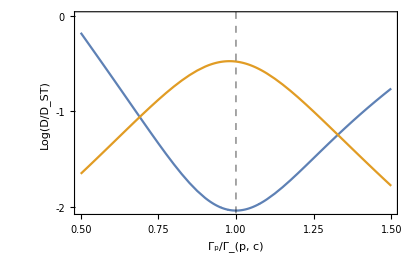

```mathematica
sweep0p95Plot = ListPlot[{{#[[1]]/lambdaBest0p95,Log[#[[2]]]}&/@linewidthPlot0p95,{#[[1]]/lambdaBest0p95,rescaleFun0p95[Re[#[[2]]]]}&/@lambdaSweep0p95}
,Frame->True
,Joined->True
,ImageSize->5.75 72
,FrameLabel->{{"Log(D/D_ST)",Rotate["⟨n⟩",π]},{"Γ_p/Γ_(p, c)",None}}
,GridLines->{{{1.0,Directive[Black,Dashed,Opacity[1]]}},None}
,FrameTicks->{{{-5,-4,-3,-2,-1,0},{{rescaleFun0p95[800],800},{rescaleFun0p95[600],600},{rescaleFun0p95[400],400},{rescaleFun0p95[200],200}}},Automatic}
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Cambria"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Cambria"]},{Directive[Black,FontSize->16,FontFamily->"Cambria"],Directive[Black,FontSize->16,FontFamily->"Cambria"]}}
]
```

```mathematica
Monitor[
lambdaSweep0p95Redo =Table[
resTemp = tempfun3[ratio  lambdaBest0p95,0.95gBest];
Flatten[{ratio lambdaBest0p95,resTemp},1]
,{ratio,0.8,1.2,0.1}];
,ratio]
lambdaSweep0p95RedoDist =  Table[
Chop[Diagonal[partialTraceAtom[lambdaSweep0p95Redo[[j,-1]]]]]
,{j,Length[lambdaSweep0p95Redo]}];
```

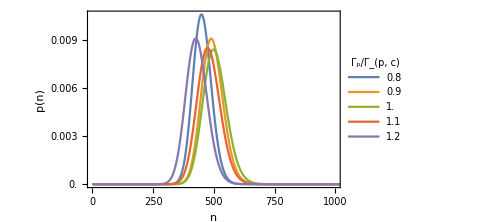

```mathematica
g1dist0p95Plot=ListPlot[lambdaSweep0p95RedoDist
,ImageSize->5 72
,FrameLabel->{"n","p(n)"}
,Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->{{0,1000},Full}
,FrameTicks->{{{0.0,0.003,0.006,0.009},None},{Automatic,Automatic}}
(*,PlotLegends->(Style["Γ_p/Γ_1 = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@lambdaSweep[[posList,1]])*)
,PlotLegends->Placed[
LineLegend[lambdaSweep0p95Redo[[All,1]]/lambdaBest0p95,LegendLabel->"Γ_p/Γ_(p, c)",LabelStyle->Directive[Black,14,FontFamily->"Cambria"],LegendFunction->(Framed[#1,RoundingRadius->5,FrameStyle->Directive[Black,Thin]]&)]
,{0.85,0.5}]
,Joined->True]
```

```mathematica
generateBops[phic_,bigPhi_,rac_,nMax_?IntegerQ,m0_?IntegerQ]:=Module[{Aop1,Aop2},
Quiet[Aop1 = bigPhi Exp[-phic^2/2](1.0 phic aop+Sum[(-1.0)^j phic^(2j+1)/(Factorial[j] Factorial[j+1])MatrixPower[aopᵀ,j].MatrixPower[aop,j+1],{j,1,nMax}])];
Aop2 =2 rac phic aop;

Bopc=Aop1+Aop2;
Bopc=Bopc/(Diagonal[Bopc,1][[m0]]);
]
```

```mathematica
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
```

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
Return[Factorial[m]/Factorial[m-n]]
]
```

```mathematica
Aelem[m_?IntegerQ,rac_?NumericQ,zc_?NumericQ]:=Module[{ϕc,expϕc},
ϕc =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
expϕc=Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
Quiet[ϕc √(m+1) (bigPhi Exp[-ϕc^2/2]Sum[(-1)^n ϕc^(2n)/(1.0 Factorial[n] Factorial[n+1])bracketN[m,n],{n,0,m}]+2 rac)]
]
```

```mathematica
findMinN[zc_?NumericQ,rac_?NumericQ]:=Module[{tbAelem,tbAelemDiff,pos},
tbAelem = ParallelTable[ Aelem[j,rac,zc],{j,0,3000}];
tbAelemDiff=tbAelem[[2;;]]-tbAelem[[;;-2]];

pos=Position[tbAelemDiff,Min[tbAelemDiff]][[1,1]];

Return[{pos+1,tbAelem}]
]
```

```mathematica
zc1000 = x/.(NSolve[fit[1/x] == 1000,x][[1]])
```

6.3597

```mathematica
generateBops[zc_,rac_,nMax_?IntegerQ]:=Module[{m0,tbBelem},
{m0,tbBelem} = findMinN[zc,rac];

Bopc=SparseArray[DiagonalMatrix[1/tbBelem[[m0]] tbBelem[[;;nMax]],1],{nMax+1,nMax+1}]; 
BopcD=SparseArray[DiagonalMatrix[1/tbBelem[[m0]] tbBelem[[;;nMax]],-1],{nMax+1,nMax+1}];

BOpc= KroneckerProduct[Bopc,IdentityMatrix[2]];
BOpcD=KroneckerProduct[BopcD,IdentityMatrix[2]];
]
```

```mathematica
coord =Union[ Range[0.419,0.425,0.0005], Range[0.425,0.43,0.001],Range[0.43,0.5,0.01]]
coord//Length
```

{0.419,0.4195,0.42,0.4205,0.421,0.4215,0.422,0.4225,0.423,0.4235,0.424,0.4245,0.425,0.426,0.427,0.428,0.429,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5}

25

```mathematica
coord3=Complement[ Range[0.43,0.44,0.001], coord]
coord3//Length
```

{0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439}

9

```mathematica
bopDir = FileNameJoin[{saveDir,"b_ops"}];
If[Not[DirectoryQ[bopDir]],CreateDirectory[bopDir]]
```

C:\Dropbox\Input_output_theory\Laser_theory\Clean_codes_for_paper\testing\b_ops

```mathematica
Monitor[
Do[
generateBops[zc1000,coord[[j]],2500];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord[[j]]]<>".m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,{Bopc,BopcD,BOpc,BOpcD}];
,{j,Length[coord]}]
,j]
```

```mathematica
coord2 =Union[ Range[0.417,0.41,-0.001], Range[0.41,0.35,0.0025]]
coord2//Length
```

{0.41,0.411,0.412,0.413,0.414,0.415,0.416,0.417}

8

```mathematica
Monitor[
Do[
generateBops[zc1000,coord2[[j]],2500];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord2[[j]]]<>".m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,{Bopc,BopcD,BOpc,BOpcD}];
,{j,Length[coord2]}]
,j]
```

```mathematica
coord3=Complement[ Range[0.43,0.44,0.001], coord]
coord3//Length
```

{0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439}

9

```mathematica
Monitor[
Do[
generateBops[zc1000,coord3[[j]],2500];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[j]]]<>".m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,{Bopc,BopcD,BOpc,BOpcD}];
,{j,Length[coord3]}]
,j]
```

```mathematica
iOp = IdentityMatrix[Length[AOpc],SparseArray];
```

```mathematica
Monitor[
Do[
generateBops[zc1000,coord[[j]],2500];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord[[j]]]<>".m"}];
Get[fn];
lossSO = -1/2(projectorD.combineOps[BOpcᵀ.BOpc,iOp].projector+projectorD.combineOps[iOp,BOpcᵀ.BOpc].projector-2 projectorD.combineOps[BOpc,BOpcᵀ].projector);
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord[[j]]]<>"_loss.m"}];
Save[fn,lossSO];
,{j,Length[coord]}]
,j]
```

```mathematica
Monitor[
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord2[[j]]]<>".m"}];
Get[fn];
lossSO = -1/2(projectorD.combineOps[BOpcᵀ.BOpc,iOp].projector+projectorD.combineOps[iOp,BOpcᵀ.BOpc].projector-2 projectorD.combineOps[BOpc,BOpcᵀ].projector);
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord2[[j]]]<>"_loss.m"}];
Save[fn,lossSO];
,{j,Length[coord2]}]
,j]
```

```mathematica
Monitor[
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[j]]]<>".m"}];
Get[fn];
lossSO = -1/2(projectorD.combineOps[BOpcᵀ.BOpc,iOp].projector+projectorD.combineOps[iOp,BOpcᵀ.BOpc].projector-2 projectorD.combineOps[BOpc,BOpcᵀ].projector);
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[j]]]<>"_loss.m"}];
Save[fn,lossSO];
,{j,Length[coord3]}]
,j]
```

```mathematica
mesh = Table[
{lambda,gmesh gBest}
,{lambda,2.5,5.5,0.05}
,{gmesh,0.9,1.1,0.01}];
mesh = Flatten[mesh,1];
mesh//Dimensions
```

{1281,2}

```mathematica
sweepDir = FileNameJoin[{saveDir,"sweep_data"}];
If[Not[DirectoryQ[sweepDir]],CreateDirectory[sweepDir]]
```

C:\Dropbox\Input_output_theory\Laser_theory\Clean_codes_for_paper\testing\sweep_data

```mathematica
tempfun3[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[BOpc.steady.BOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[{nAvg,rate,Log[Abs[ev[[-2]]]],steady}]
]
```

```mathematica
Monitor[
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord[[j]]]<>".m"}];
Get[fn];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord[[j]]]<>"_loss.m"}];
Get[fn];

meshSweepSol = ParallelTable[
{x,y} = mesh[[k]];
resTemp = tempfun3[x,y];
Flatten[{x,y,resTemp[[;;-2]]}]
,{k,Length[mesh]}];

fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord[[j]]]<>"_meshSweepSol.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,meshSweepSol];
linewidthChangeRPlot2D= {#[[1]],#[[2]],Chop[Exp[#[[5]]]/(Abs[#[[4]]]/(4 Abs[#[[3]]]^2))]}&/@meshSweepSol;
fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord[[j]]]<>"_linewidth.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,linewidthChangeRPlot2D];

sweepMaxG = Table[
lineTemp = Select[linewidthChangeRPlot2D,#[[2]] == x&];
SortBy[lineTemp,#[[-1]]&][[1]]
,{x,0.9 gBest,1.1 gBest,0.01 gBest}];

fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord[[j]]]<>"_sweepMaxG.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,sweepMaxG];

,{j,Length[coord]}];
,j]
```

```mathematica
Monitor[
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord2[[j]]]<>".m"}];
Get[fn];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord2[[j]]]<>"_loss.m"}];
Get[fn];

meshSweepSol = ParallelTable[
{x,y} = mesh[[k]];
resTemp = tempfun3[x,y];
Flatten[{x,y,resTemp[[;;-2]]}]
,{k,Length[mesh]}];

fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord2[[j]]]<>"_meshSweepSol.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,meshSweepSol];
linewidthChangeRPlot2D= {#[[1]],#[[2]],Chop[Exp[#[[5]]]/(Abs[#[[4]]]/(4 Abs[#[[3]]]^2))]}&/@meshSweepSol;
fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord2[[j]]]<>"_linewidth.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,linewidthChangeRPlot2D];

sweepMaxG = Table[
lineTemp = Select[linewidthChangeRPlot2D,#[[2]] == x&];
SortBy[lineTemp,#[[-1]]&][[1]]
,{x,0.9 gBest,1.1 gBest,0.01 gBest}];

fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord2[[j]]]<>"_sweepMaxG.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,sweepMaxG];

,{j,Length[coord2]}];
,j]
```

```mathematica
coord3
```

{0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439}

```mathematica
Monitor[
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[j]]]<>".m"}];
Get[fn];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[j]]]<>"_loss.m"}];
Get[fn];

meshSweepSol = ParallelTable[
{x,y} = mesh[[k]];
resTemp = tempfun3[x,y];
Flatten[{x,y,resTemp[[;;-2]]}]
,{k,Length[mesh]}];

fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord3[[j]]]<>"_meshSweepSol.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,meshSweepSol];
linewidthChangeRPlot2D= {#[[1]],#[[2]],Chop[Exp[#[[5]]]/(Abs[#[[4]]]/(4 Abs[#[[3]]]^2))]}&/@meshSweepSol;
fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord3[[j]]]<>"_linewidth.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,linewidthChangeRPlot2D];

sweepMaxG = Table[
lineTemp = Select[linewidthChangeRPlot2D,#[[2]] == x&];
SortBy[lineTemp,#[[-1]]&][[1]]
,{x,0.9 gBest,1.1 gBest,0.01 gBest}];

fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord3[[j]]]<>"_sweepMaxG.m"}];
If[FileExistsQ[fnSweep],DeleteFile[fnSweep]];
Save[fnSweep,sweepMaxG];

,{j,Length[coord3]}];
,j]
```

```mathematica
bestLWdiffR= {}
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord[[j]]]<>".m"}];
Get[fn];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord[[j]]]<>"_loss.m"}];
Get[fn];
fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord[[j]]]<>"_meshSweepSol.m"}];
Get[fnSweep];

AppendTo[bestLWdiffR,Flatten[{coord[[j]],SortBy[meshSweepSol,#[[5]]&][[1]]}]]
,{j,Length[coord]}]
```

{}

```mathematica
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord2[[j]]]<>".m"}];
Get[fn];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord2[[j]]]<>"_loss.m"}];
Get[fn];
fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord2[[j]]]<>"_meshSweepSol.m"}];
Get[fnSweep];

AppendTo[bestLWdiffR,Flatten[{coord2[[j]],SortBy[meshSweepSol,#[[-1]]&][[1]]}]]
,{j,Length[coord2]}]
```

```mathematica
Do[
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[j]]]<>".m"}];
Get[fn];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[j]]]<>"_loss.m"}];
Get[fn];
fnSweep = FileNameJoin[{sweepDir,"2D_sweep_r_"<>ToString[coord3[[j]]]<>"_meshSweepSol.m"}];
Get[fnSweep];

AppendTo[bestLWdiffR,Flatten[{coord3[[j]],SortBy[meshSweepSol,#[[-1]]&][[1]]}]]
,{j,Length[coord3]}]
```

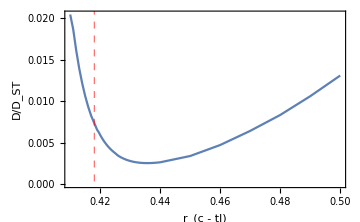

```mathematica
ListPlot[Sort[{#[[1]],Abs[Exp[#[[6]]]/((#[[5]])/(4 (#[[4]])^2))]}&/@bestLWdiffR],Joined->True,PlotRange->Full,Frame->True
,FrameLabel->{"r_(c - tl)","D/D_ST"}
,PlotRange->{{0.409,0.501},Full}
,GridLines->{{{0.418,Directive[Red,Dashed,Opacity[1]]}},None}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,ImageSize->5 72]
```

```mathematica
distIndex = Flatten[Position[bestLWdiffR[[All,1]],#]&/@{0.41,0.419,0.436,0.48}]
```

{26,1,39,23}

```mathematica
iOp = IdentityMatrix[Length[AOpc],SparseArray];
lossSO = -1/2(projectorD.combineOps[AOpcᵀ.AOpc,iOp].projector+projectorD.combineOps[iOp,AOpcᵀ.AOpc].projector-2 projectorD.combineOps[AOpc,AOpcᵀ].projector);

optimum = tempfun3[lambdaBest,gBest];
```

```mathematica
optimum
```

{1079.03+1.70918×10^-8 ⅈ,1.00452+9.93179×10^-13 ⅈ,-20.2698,SparseArray[…]}

```mathematica
Monitor[
distributionList = Table[
rValue = bestLWdiffR[[j,1]];

fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[rValue]<>".m"}];
Get[fn];
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[rValue]<>"_loss.m"}];
Get[fn];

resTemp = tempfun3[bestLWdiffR[[j,2]],bestLWdiffR[[j,3]]];

cavity = partialTraceAtom[resTemp[[-1]]];

Diagonal[cavity]
,{j,Length[bestLWdiffR]}
];
,j]
```

```mathematica
distributionPlotData = Transpose[{Range[Length[#]]-1,#}]&/@{Chop[distributionList[[distIndex[[1]]]]],Chop[Diagonal[partialTraceAtom[optimum[[-1]]]]],Chop[distributionList[[distIndex[[3]]]]],Chop[distributionList[[distIndex[[4]]]]]};
```

```mathematica
reScale[x_]:=(0.006-0.001)/(1.1-0.85)(x-0.85)
```

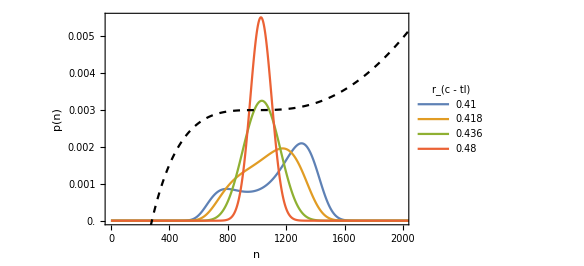

```mathematica
distPlot = Show[
ListPlot[distributionPlotData
,PlotRange->{{0,2000},Full}
,Joined->True
,Frame->True
,FrameLabel->{{"p(n)",Rotate["⟨n|A_(c,m_0)|n+1⟩",π]},{"n",None}}
,FrameTicks->{{{0.000,0.001,0.002,0.003,0.004,0.005},{{reScale[0.8],0.8},{reScale[0.9],0.9},{reScale[1.0],1.0},{reScale[1.1],1.1},{reScale[1.2],1.2}}},{Automatic,Automatic}}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotLegends->Placed[
LineLegend[{0.41,0.418,0.436,0.48},LegendLabel->"r_(c - tl)",LabelStyle->Directive[Black,14,FontFamily->"Cambria"],LegendFunction->(Framed[#1,RoundingRadius->5,FrameStyle->Directive[Black,Thin],Background->White]&)]
,{0.2,0.6}]
,ImageSize->6 72
]
,ListPlot[Transpose[{Range[Length[Aopc]-1]-1,Normal[reScale[Diagonal[Aopc,1]]]}]
,Joined->True
,PlotStyle->{Black,Dashed}
,PlotRange->Full
]
]
```

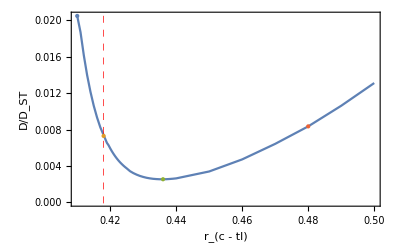

```mathematica
sweepRPlot=Show[
ListPlot[Sort[{#[[1]],Abs[Exp[#[[6]]]/((#[[5]])/(4 (#[[4]])^2))]}&/@bestLWdiffR],Joined->True,PlotRange->Full,Frame->True
,FrameLabel->{"r_(c - tl)","D/D_ST"}
,PlotRange->{{0.409,0.501},Full}
,GridLines->{{{0.418,Directive[Red,Dashed,Opacity[1]]}},None}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,ImageSize->5.5 72],
Graphics[{ColorData[97][1],PointSize[Large],Point[{#[[1]],Abs[Exp[#[[6]]]/((#[[5]])/(4 (#[[4]])^2))]}&@(bestLWdiffR[[distIndex[[1]]]])]}]
,Graphics[{ColorData[97][2],PointSize[Large],Point[{0.418,Abs[Exp[optimum[[3]]]/(optimum[[2]]/(4 optimum[[1]]^2))]}]}]
,Graphics[{ColorData[97][3],PointSize[Large],Point[{#[[1]],Abs[Exp[#[[6]]]/((#[[5]])/(4 (#[[4]])^2))]}&@(bestLWdiffR[[distIndex[[3]]]])]}]
,Graphics[{ColorData[97][4],PointSize[Large],Point[{#[[1]],Abs[Exp[#[[6]]]/((#[[5]])/(4 (#[[4]])^2))]}&@(bestLWdiffR[[distIndex[[4]]]])]}]
]
```

```mathematica
fn = FileNameJoin[{bopDir,"new_Bops_"<>ToString[coord3[[6]]]<>".m"}];
Get[fn];
```

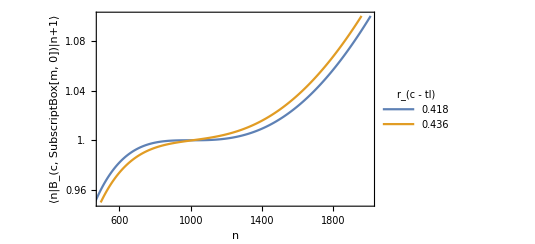

```mathematica
plt=ListPlot[{Diagonal[Aopc,1],Diagonal[Bopc,1]},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,ImageSize->5.5 72
,Joined->True
,PlotRange->{{500,2000},{0.95,1.1}}
,FrameTicks->{{{0.96,1.00,1.04,1.08},Automatic},{{600,1000,1400,1800},Automatic}}
,FrameLabel->{"n","⟨n|B_(c, SubscriptBox[m, 0])|n+1⟩"}
,PlotLegends->Placed[
LineLegend[{0.418,coord3[[6]]},LegendLabel->"r_(c - tl)",LabelStyle->Directive[Black,14,FontFamily->"Cambria"],LegendFunction->(Framed[#1,RoundingRadius->5,FrameStyle->Directive[Black,Thin]]&)]
,{0.2,0.75}]]
```

```mathematica
tempfun2[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
sopDir =saveDir;
```

```mathematica
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[500]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];
```

```mathematica
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
res1
```

{-18.2014,{x→3.63664,y→1.00246}}

```mathematica
lambdaBest = x/.res1[[2]]
```

3.63664

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
tempfun[3.5,1.0]
```

-18.0446

```mathematica
gBest = y x/2 √(1.0/(x- 2))/.res1[[2]]
```

1.42483

```mathematica
gSweepCrude = Range[0.9,1.1,0.005] gBest;
gSweepFine = Range[0.99,1.01,0.001]gBest;
gSweepCoord = Union[gSweepCrude,gSweepFine]
```

{1.28234,1.28947,1.29659,1.30372,1.31084,1.31797,1.32509,1.33221,1.33934,1.34646,1.35359,1.36071,1.36783,1.37496,1.38208,1.38921,1.39633,1.40345,1.41058,1.412,1.41343,1.41485,1.41628,1.4177,1.41913,1.42055,1.42198,1.4234,1.42483,1.42625,1.42768,1.4291,1.43053,1.43195,1.43195,1.43338,1.4348,1.43623,1.43765,1.43908,1.4462,1.45332,1.46045,1.46757,1.4747,1.48182,1.48894,1.49607,1.50319,1.51032,1.51744,1.52456,1.53169,1.53881,1.54594,1.55306,1.56019,1.56731}

```mathematica
projCavityg = KroneckerProduct[IdentityMatrix[Length[aop],SparseArray],{1,0}];
projCavityg//Dimensions
```

{1251,2502}

```mathematica
projCavitye = KroneckerProduct[IdentityMatrix[Length[aop],SparseArray],{0,1}];
projCavitye//Dimensions
```

{1251,2502}

```mathematica
partialTraceAtom[mtx_]:=Module[{},
Return[projCavityg.mtx.projCavitygᵀ+projCavitye.mtx.projCavityeᵀ]
]
```

```mathematica
Monitor[
bestLambdaList = Table[
resTemp = FindMinimum[Re[tempfun2[x,gSweepCoord[[j]]]],{x,2.7,4.0}(*,PrecisionGoal->5,AccuracyGoal->5*)];
x/.resTemp[[2]]
,{j,Length[gSweepCoord]}];
,j]
```

```mathematica
tempfun3[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[{nAvg,rate,Log[Abs[ev[[-2]]]],steady}]
]
```

```mathematica
allCoord = Transpose[{gSweepCoord,bestLambdaList}];
Print["allCoord length = ",ToString[Length[allCoord]]];
Monitor[
bestSweepRes = Table[
Flatten[{allCoord[[j]],tempfun3[allCoord[[j,2]],allCoord[[j,1]]]},1]
,{j,Length[allCoord]}];
,j]
```

allCoord length = 58

```mathematica
rescaleFun3[x_]:=(4.5/(600-100))(x-600)
```

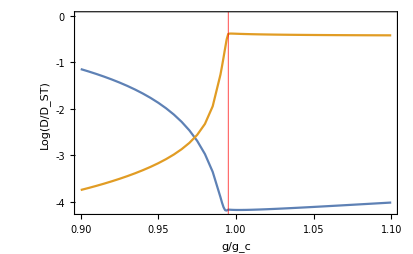

```mathematica
bestPlot = ListPlot[{{(#[[1]])/gBest,Log[Exp[#[[5]]]/Abs[(#[[4]])/(4 (#[[3]])^2)]]}&/@bestSweepRes,{#[[1]]/gBest,rescaleFun3[Re[#[[3]]]]}&/@bestSweepRes}
,Frame->True
,Joined->True
,ImageSize->5.75 72
,FrameLabel->{{"Log(D/D_ST)",Rotate["⟨n⟩",π]},{"g/g_c",None}}
,GridLines->{{{0.995,Directive[Red,Opacity[1]]}},None}
,FrameTicks->{{{-5,-4,-3,-2,-1,0},{{rescaleFun3[600],600},{rescaleFun3[500],500},{rescaleFun3[400],400},{rescaleFun3[300],300},{rescaleFun3[200],200}}},Automatic}
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Cambria"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Cambria"]},{Directive[Black,FontSize->16,FontFamily->"Cambria"],Directive[Black,FontSize->16,FontFamily->"Cambria"]}}]
```

## Perturb m_0

```mathematica
ϕ0 = Quantity["ReducedPlanckConstant"]/(2Quantity["ElementaryCharge"])
```

1/2 ℏ/e

```mathematica
combineOps[op1_,op2_]:=Module[{top},
top = TensorProduct[op1,op2];
top = Flatten[Transpose[top,{1,3,4,2}],1];
top = Flatten[Transpose[top,{3,1,2}],1];
Return[topᵀ]
]
```

```mathematica
updateABOCCopsNew[zc_?NumericQ]:=Module[{},
m0=Round[fit[1/zc]];
maxN = Round[2.5 m0];


aTrunc =Floor[maxN];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],
SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))];
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

generateAops[phic,bigPhi,0.418,maxN,m0];
AopcD=Aopcᵀ;

AOpc= KroneckerProduct[Aopc,SparseArray[IdentityMatrix[2]]];
AOpcD=KroneckerProduct[AopcD,SparseArray[IdentityMatrix[2]]];
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( projectorD.combineOps[hac,iOp].projector-projectorD.combineOps[iOp,hac].projector);
pumpSO = -1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2projectorD.combineOps[sP,sM].projector);
normalLossSO = -1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2 projectorD.combineOps[aOp,aOpᵀ].projector);
lossSO = -1/2(projectorD.combineOps[AOpcᵀ.AOpc,iOp].projector+projectorD.combineOps[iOp,AOpcᵀ.AOpc].projector-2 projectorD.combineOps[AOpc,AOpcᵀ].projector);
Speak["Operators are updated."]
]
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
tempFun2[lambda_?NumericQ,gr_?NumericQ]:=Module[{γ,g},

γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{nAvg,rate}]
]
```

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third,fourth,fifth},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[dim-3],Range[4,dim]}],Transpose[{Range[4,dim],Range[dim-3]}]];

fourth = Join[Transpose[{Range[dim-4],Range[5,dim]}],Transpose[{Range[5,dim],Range[dim-4]}]];

fifth = Join[Transpose[{Range[1,dim-5,2],Range[6,dim,2]}], Transpose[{Range[6,dim,2],Range[1,dim-5,2]}]];

Return[Join[center,first,second,third,fourth,fifth]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

```mathematica
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[1000]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];
```

```mathematica
tempfun3[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[{nAvg,rate,Log[Abs[ev[[-2]]]],steady}]
]
```

```mathematica
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
res1
```

{-20.2698,{x→3.5,y→1.0013}}

```mathematica
gBest = y x/2 √(1.0/(x- 2))/.res1[[2]]
```

1.43073

```mathematica
lambdaCrude= Range[2.5,5.5,0.05];
lambdaFine1 = Range[3.45,3.55,0.01];
lambdaFine2 = Range[4.65,4.75,0.01];
lambdaCoord = Union[lambdaCrude,lambdaFine1,lambdaFine2];
Length[lambdaCoord]
```

77

```mathematica
lambdaBest = x/.res1[[2]]
```

3.5

```mathematica
gSweepCrude = Range[0.9,1.1,0.005] gBest;
gSweepFine = Range[0.99,1.01,0.001]gBest;
gSweepCoord = Union[gSweepCrude,gSweepFine]
```

{1.28765,1.2948,1.30196,1.30911,1.31626,1.32342,1.33057,1.33772,1.34488,1.35203,1.35918,1.36634,1.37349,1.38065,1.3878,1.39495,1.40211,1.40926,1.41641,1.41784,1.41928,1.42071,1.42214,1.42357,1.425,1.42643,1.42786,1.42929,1.43072,1.43215,1.43358,1.43501,1.43644,1.43787,1.43787,1.43931,1.44074,1.44217,1.4436,1.44503,1.45218,1.45934,1.46649,1.47364,1.4808,1.48795,1.4951,1.50226,1.50941,1.51656,1.52372,1.53087,1.53803,1.54518,1.55233,1.55949,1.56664,1.57379}

```mathematica
tempfun3[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[{nAvg,rate,Log[Abs[ev[[-2]]]],steady}]
]
```

```mathematica
updateABOCCopsNew[zc_?NumericQ]:=Module[{},
m0=Round[fit[1/zc]];
maxN = Round[2.5 m0];


aTrunc =Floor[maxN];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],
SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))];
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

generateAops[phic,bigPhi,0.418,maxN,m0];
AopcD=Aopcᵀ;

AOpc= KroneckerProduct[Aopc,SparseArray[IdentityMatrix[2]]];
AOpcD=KroneckerProduct[AopcD,SparseArray[IdentityMatrix[2]]];
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( projectorD.combineOps[hac,iOp].projector-projectorD.combineOps[iOp,hac].projector);
pumpSO = -1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2projectorD.combineOps[sP,sM].projector);
normalLossSO = -1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2 projectorD.combineOps[aOp,aOpᵀ].projector);
lossSO = -1/2(projectorD.combineOps[AOpcᵀ.AOpc,iOp].projector+projectorD.combineOps[iOp,AOpcᵀ.AOpc].projector-2 projectorD.combineOps[AOpc,AOpcᵀ].projector);
Speak["Operators are updated."]
]
```

```mathematica
generateBops[phic_,bigPhi_,rac_,nMax_?IntegerQ,m0_?IntegerQ]:=Module[{Aop1,Aop2},
Quiet[Aop1 = bigPhi Exp[-phic^2/2](1.0 phic aop+Sum[(-1.0)^j phic^(2j+1)/(Factorial[j] Factorial[j+1])MatrixPower[aopᵀ,j].MatrixPower[aop,j+1],{j,1,nMax}])];
Aop2 =2 rac phic aop;

Bopc=Aop1+Aop2;
Bopc=Bopc/(Diagonal[Bopc,1][[m0]]);
]
```

```mathematica
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
```

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
Return[Factorial[m]/Factorial[m-n]]
]
```

```mathematica
Aelem[m_?IntegerQ,rac_?NumericQ,zc_?NumericQ]:=Module[{ϕc,expϕc},
ϕc =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
expϕc=Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
Quiet[ϕc √(m+1) (bigPhi Exp[-ϕc^2/2]Sum[(-1)^n ϕc^(2n)/(1.0 Factorial[n] Factorial[n+1])bracketN[m,n],{n,0,m}]+2 rac)]
]
```

```mathematica
findMinN[zc_?NumericQ,rac_?NumericQ]:=Module[{tbAelem,tbAelemDiff,pos},
tbAelem = ParallelTable[ Aelem[j,rac,zc],{j,0,3000}];
tbAelemDiff=tbAelem[[2;;]]-tbAelem[[;;-2]];

pos=Position[tbAelemDiff,Min[tbAelemDiff]][[1,1]];

Return[{pos+1,tbAelem}]
]
```

```mathematica
AbsoluteTiming[
{m0,tbAelem} = findMinN[zc1000,0.418];
]
```

{149.505,Null}

```mathematica
generateBops[zc_,rac_,nMax_?IntegerQ]:=Module[{m0,tbBelem},
{m0,tbBelem} = findMinN[zc,rac];

Bopc=SparseArray[DiagonalMatrix[1/tbBelem[[m0]] tbBelem[[;;nMax]],1],{nMax+1,nMax+1}]; 
BopcD=SparseArray[DiagonalMatrix[1/tbBelem[[m0]] tbBelem[[;;nMax]],-1],{nMax+1,nMax+1}];

BOpc= KroneckerProduct[Bopc,IdentityMatrix[2]];
BOpcD=KroneckerProduct[BopcD,IdentityMatrix[2]];
]
```

```mathematica
iOp = IdentityMatrix[Length[AOpc],SparseArray];
```

```mathematica
mesh = Table[
{lambda,gmesh gBest}
,{lambda,2.5,5.5,0.05}
,{gmesh,0.9,1.1,0.01}];
mesh = Flatten[mesh,1];
mesh//Dimensions
```

{1281,2}

```mathematica
coord =Union[ Range[0.419,0.425,0.0005], Range[0.425,0.43,0.001],Range[0.43,0.5,0.01]];
coord3=Complement[ Range[0.43,0.44,0.001], coord];
coord2 =Union[ Range[0.417,0.41,-0.001], Range[0.41,0.35,0.0025]];
coordAll = Sort[Union[coord,coord2,coord3]];
coordAll//Length
```

42

```mathematica
tempfun4[lambda_?NumericQ,g_?NumericQ]:=Module[{γ,superOp,ev,es,steady,rate,nAvg,state,i,lw},
γ=1.;

superOp=lambda pumpSO+γ lossSO+g HacSO;{ev,es}=Eigensystem[superOp,-10];steady=SparseArray[Chop[Partition[projector.es⟦-1⟧,Length[aOp]]]];steady=steady/Tr[steady];rate=Tr[AOpc.steady.AOpcD];nAvg=Tr[Transpose[aOp].aOp.steady];

lw = 9999;
For[i=9,i≥1,i=i-1,
state =SparseArray[Chop[Partition[projector.es⟦i⟧,Length[aOp]]]];
If[
Total[Abs[Diagonal[state]]]<1.*^-8,
lw = ev[[i]] ;
Break[];
]
];

Return[{nAvg,rate,Log[Abs[lw]],10-i,steady}]]
```

```mathematica
tempfun4p[lambda_?NumericQ,g_?NumericQ]:=Module[{γ,superOp,ev,es,steady,rate,nAvg,state,i,lw},
γ=1.;

superOp=lambda pumpSO+γ lossSO+g HacSO;{ev,es}=Eigensystem[superOp,-5];

lw = 9999;
For[i=4,i≥1,i=i-1,
state =SparseArray[Chop[Partition[projector.es⟦i⟧,Length[aOp]]]];
If[
Total[Abs[Diagonal[state]]]<1.*^-8,
lw = ev[[i]] ;
Break[];
]
];

Return[Log[Abs[lw]]]]
```

```mathematica
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
res1
```

{-20.2698,{x→3.5,y→1.0013}}

```mathematica
gBest = y x/2 √(1.0/(x- 2))/.res1[[2]]
```

1.43073

```mathematica
indexL=selectElement[5002];
projector = makeProj[indexL,5002];
projectorD=Transpose[projector];
```

```mathematica
m0List = Range[550,1000,25];
Monitor[
Do[
m0T = m0List[[j]];
zTemp = x/.(NSolve[fit[1/x] == m0T,x][[1]]);
generateBops[zTemp,0.418,2500];

fn = FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,{Bopc,BopcD,BOpc,BOpcD}];

lossSO = -1/2(projectorD.combineOps[BOpcᵀ.BOpc,iOp].projector+projectorD.combineOps[iOp,BOpcᵀ.BOpc].projector-2 projectorD.combineOps[BOpc,BOpcᵀ].projector);
fn = FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,lossSO];

,{j,Length[m0List]}];
,j];
```

```mathematica
m0List2 =Round[ Range[750+12.5,1000,25]]
```

{762,788,812,838,862,888,912,938,962,988}

```mathematica
m0List3 =Round[ Range[1000+12.5,1150,12.5]]
```

{1012,1025,1038,1050,1062,1075,1088,1100,1112,1125,1138,1150}

```mathematica
Monitor[
Do[
m0T = m0List2[[j]];
zTemp = x/.(NSolve[fit[1/x] == m0T,x][[1]]);
generateBops[zTemp,0.418,2500];

fn = FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,{Bopc,BopcD,BOpc,BOpcD}];

lossSO = -1/2(projectorD.combineOps[BOpcᵀ.BOpc,iOp].projector+projectorD.combineOps[iOp,BOpcᵀ.BOpc].projector-2 projectorD.combineOps[BOpc,BOpcᵀ].projector);
fn = FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,lossSO];

,{j,Length[m0List2]}];
,j];
```

```mathematica
Monitor[
Do[
m0T = m0List3[[j]];
zTemp = x/.(NSolve[fit[1/x] == m0T,x][[1]]);
generateBops[zTemp,0.418,2500];

fn = FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,{Bopc,BopcD,BOpc,BOpcD}];

lossSO = -1/2(projectorD.combineOps[BOpcᵀ.BOpc,iOp].projector+projectorD.combineOps[iOp,BOpcᵀ.BOpc].projector-2 projectorD.combineOps[BOpc,BOpcᵀ].projector);
fn = FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}];
If[FileExistsQ[fn],DeleteFile[fn]];
Save[fn,lossSO];

,{j,Length[m0List3]}];
,j];
```

```mathematica
updateABOCCopsNew[zc1000];
```

```mathematica
Monitor[
optimumPoints = Table[
m0T = m0List[[j]];
zTemp = x/.(NSolve[fit[1/x] == m0T,x][[1]]);

Get[ FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}]];
Get[FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}]];

res4=Quiet[FindMinimum[tempfun4p[x,y],{x,3.5,3.0,4.5},{y,1.5,1.25,2.0},PrecisionGoal->2,AccuracyGoal->2]];
Print[res4];

fullRes2 = tempfun4[x/.res4[[2]],y/.res4[[2]]];

{m0T,fullRes2}
,{j,Length[m0List]}];
,j];
```

{-17.8615,{x→3.4997,y→1.49884}}

{-18.1977,{x→3.,y→1.57436}}

{-18.4216,{x→3.,y→1.56379}}

{-18.6462,{x→3.,y→1.55599}}

{-18.8694,{x→3.,y→1.55011}}

{-19.0783,{x→3.,y→1.54527}}

{-19.28,{x→3.,y→1.53905}}

{-19.4734,{x→3.,y→1.53455}}

{-19.5922,{x→3.38067,y→1.46418}}

{-19.7658,{x→3.495,y→1.45209}}

{-19.9825,{x→3.21892,y→1.47887}}

{-20.1121,{x→3.48267,y→1.44697}}

{-20.2426,{x→3.49446,y→1.44369}}

{-20.3389,{x→3.49292,y→1.44162}}

{-20.3938,{x→3.49407,y→1.43942}}

{-20.4065,{x→3.49395,y→1.43735}}

{-20.3823,{x→3.49366,y→1.43533}}

{-20.332,{x→3.49539,y→1.43314}}

{-20.2696,{x→3.49464,y→1.43109}}

```mathematica
Monitor[
FixGSweep= Table[
m0T = m0List[[j]];
zTemp = x/.(NSolve[fit[1/x] == m0T,x][[1]]);

Get[ FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}]];
Get[FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}]];

testList = ParallelTable[
test = tempfun4[x,gBest];
{x,test}
,{x,3.0,4.52,0.022}];

{m0T,testList}
,{j,Length[m0List]}];
,j];
```

```mathematica
pltData = Table[
{#[[1]],#[[2,3]]}&/@FixGSweep[[j,2]]
,{j,Length[FixGSweep]}];
```

```mathematica
ctPlotData = Table[
 {#[[1]],m0List[[j]],#[[2,3]]}&/@FixGSweep[[j,2]]
,{j,Length[m0List]}];
```

```mathematica
Monitor[
FixGSweep2= Table[
m0T = m0List[[j]];

Get[ FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}]];
Get[FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}]];

testList = ParallelTable[
test = tempfun4[x,gBest];
{x,test}
,{x,3.0,4.5,0.01}];

{m0T,testList}
,{j,9,Length[m0List]}];
,j]
```

```mathematica
pltData2 = Table[
{#[[1]],#[[2,3]]}&/@FixGSweep2[[j,2]]
,{j,Length[FixGSweep2]}];
```

```mathematica
ctPlotData2 = Table[
 {#[[1]],m0List[[8+j]],#[[2,3]]}&/@FixGSweep2[[j,2]]
,{j,Length[m0List]-8}];
```

```mathematica
ctPlotData2p = Table[
{#[[1]],m0List[[8+j]],If[#[[2,4]]==1,#[[2,3]],Log[9999]]}&/@FixGSweep2[[j,2]]
,{j,Length[m0List]-8}];
```

```mathematica
Monitor[
FixGSweep3= Table[
m0T = m0List2[[j]];

Get[ FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}]];
Get[FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}]];

testList = ParallelTable[
test = tempfun4[x,gBest];
{x,test}
,{x,3.0,4.5,0.01}];

{m0T,testList}
,{j,Length[m0List2]}];
,j]
```

```mathematica
ctPlotData3 = Table[
 {#[[1]],m0List2[[j]],#[[2,3]]}&/@FixGSweep3[[j,2]]
,{j,Length[m0List2]}];
```

```mathematica
ctPlotData3pp = Table[
temp= FixGSweep3[[j,2]];
temp1 = Select[temp,#[[1]]>4.0&];
temp1 = SortBy[temp1,#[[1]]&];
temp2 = Select[temp,#[[1]]≤4.0&];
temp2 = Reverse[SortBy[temp2,#[[1]]&]];

list1 = {};
For[k=1,k≤Length[temp1],k=k+1,
If[temp1[[k,2,4]]==1,
AppendTo[list1,{temp1[[k,1]],m0List2[[j]],temp1[[k,2,3]]}],
Break[]
]
];
While[k≤Length[temp1],
AppendTo[list1,{temp1[[k,1]],m0List2[[j]],Log[9999]}];
k=k+1
];

For[k=1,k≤Length[temp2],k=k+1,
If[temp2[[k,2,4]]==1,
AppendTo[list1,{temp2[[k,1]],m0List2[[j]],temp2[[k,2,3]]}],
Break[]
]
];
While[k≤Length[temp2],
AppendTo[list1,{temp2[[k,1]],m0List2[[j]],Log[9999]}];
k=k+1
];

list1
,{j,Length[m0List2]}];
```

```mathematica
ctPlotData2pp = Table[
temp= FixGSweep2[[j,2]];
temp1 = Select[temp,#[[1]]>4.0&];
temp1 = SortBy[temp1,#[[1]]&];
temp2 = Select[temp,#[[1]]≤4.0&];
temp2 = Reverse[SortBy[temp2,#[[1]]&]];

list1 = {};
For[k=1,k≤Length[temp1],k=k+1,
If[temp1[[k,2,4]]==1,
AppendTo[list1,{temp1[[k,1]],m0List[[8+j]],temp1[[k,2,3]]}],
Break[]
]
];
While[k≤Length[temp1],
AppendTo[list1,{temp1[[k,1]],m0List[[8+j]],Log[9999]}];
k=k+1
];

For[k=1,k≤Length[temp2],k=k+1,
If[temp2[[k,2,4]]==1,
AppendTo[list1,{temp2[[k,1]],m0List[[8+j]],temp2[[k,2,3]]}],
Break[]
]
];
While[k≤Length[temp2],
AppendTo[list1,{temp2[[k,1]],m0List[[8+j]],Log[9999]}];
k=k+1
];

list1
,{j,Length[m0List]-8}];
```

```mathematica
Get[ FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[900]<>".m"}]];
Get[FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[900]<>"_loss.m"}]];
```

```mathematica
ctPlotData3ppp = Table[
temp= FixGSweep3[[j,2]];
temp1 = Select[temp,#[[1]]>4.0&];
temp1 = SortBy[temp1,#[[1]]&];
temp2 = Select[temp,#[[1]]≤4.0&];
temp2 = Reverse[SortBy[temp2,#[[1]]&]];

list1 = {};
For[k=1,k≤Length[temp1],k=k+1,
If[temp1[[k,2,4]]==1,
AppendTo[list1,{temp1[[k,1]],m0List2[[j]],Log[Abs[Exp[temp1[[k,2,3]]]/(temp1[[k,2,2]]/(4 temp1[[k,2,1]]^2))]]}],
Break[]
]
];
While[k≤Length[temp1],
AppendTo[list1,{temp1[[k,1]],m0List2[[j]],Log[9999]}];
k=k+1
];

For[k=1,k≤Length[temp2],k=k+1,
If[temp2[[k,2,4]]==1,
AppendTo[list1,{temp2[[k,1]],m0List2[[j]],Log[Abs[Exp[temp2[[k,2,3]]]/(temp2[[k,2,2]]/(4 temp2[[k,2,1]]^2))]]}],
Break[]
]
];
While[k≤Length[temp2],
AppendTo[list1,{temp2[[k,1]],m0List2[[j]],Log[9999]}];
k=k+1
];

list1
,{j,Length[m0List2]}];
```

```mathematica
ctPlotData2ppp = Table[
temp= FixGSweep2[[j,2]];
temp1 = Select[temp,#[[1]]>4.0&];
temp1 = SortBy[temp1,#[[1]]&];
temp2 = Select[temp,#[[1]]≤4.0&];
temp2 = Reverse[SortBy[temp2,#[[1]]&]];

list1 = {};
For[k=1,k≤Length[temp1],k=k+1,
If[temp1[[k,2,4]]==1,
AppendTo[list1,{temp1[[k,1]],m0List[[8+j]],Log[Abs[Exp[temp1[[k,2,3]]]/(temp1[[k,2,2]]/(4 temp1[[k,2,1]]^2))]]}],
Break[]
]
];
While[k≤Length[temp1],
AppendTo[list1,{temp1[[k,1]],m0List[[8+j]],Log[9999]}];
k=k+1
];

For[k=1,k≤Length[temp2],k=k+1,
If[temp2[[k,2,4]]==1,
AppendTo[list1,{temp2[[k,1]],m0List[[8+j]],Log[Abs[Exp[temp2[[k,2,3]]]/(temp2[[k,2,2]]/(4 temp2[[k,2,1]]^2))]]}],
Break[]
]
];
While[k≤Length[temp2],
AppendTo[list1,{temp2[[k,1]],m0List[[8+j]],Log[9999]}];
k=k+1
];

list1
,{j,Length[m0List]-8}];
```

```mathematica
Monitor[
FixGSweep4= Table[
m0T = m0List3[[j]];

Get[ FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>".m"}]];
Get[FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[m0T]<>"_loss.m"}]];

testList = ParallelTable[
test = tempfun4[x,gBest];
{x,test}
,{x,3.0,4.5,0.01}];

{m0T,testList}
,{j,Length[m0List3]}];
,j]
```

```mathematica
ctPlotData4pp = Table[
temp= FixGSweep4[[j,2]];
temp1 = Select[temp,#[[1]]>4.0&];
temp1 = SortBy[temp1,#[[1]]&];
temp2 = Select[temp,#[[1]]≤4.0&];
temp2 = Reverse[SortBy[temp2,#[[1]]&]];

list1 = {};
For[k=1,k≤Length[temp1],k=k+1,
If[temp1[[k,2,4]]==1,
AppendTo[list1,{temp1[[k,1]],m0List3[[j]],temp1[[k,2,3]]}],
Break[]
]
];
While[k≤Length[temp1],
AppendTo[list1,{temp1[[k,1]],m0List3[[j]],Log[9999]}];
k=k+1
];

For[k=1,k≤Length[temp2],k=k+1,
If[temp2[[k,2,4]]==1,
AppendTo[list1,{temp2[[k,1]],m0List3[[j]],temp2[[k,2,3]]}],
Break[]
]
];
While[k≤Length[temp2],
AppendTo[list1,{temp2[[k,1]],m0List3[[j]],Log[9999]}];
k=k+1
];

list1
,{j,Length[m0List3]}];
```

```mathematica
ctPlotDataCombpp = Join[Flatten[ctPlotData2pp,1],Flatten[ctPlotData3pp,1],Flatten[ctPlotData4pp,1]];
```

```mathematica
ctPlotDataCombppMod = {}
Do[
If[ctPlotDataCombpp[[j,1]]==3.11&&ctPlotDataCombpp[[j,2]]==900,
Continue[],
AppendTo[ctPlotDataCombppMod,ctPlotDataCombpp[[j]]]
]
,{j,Length[ctPlotDataCombpp]}];
```

{}

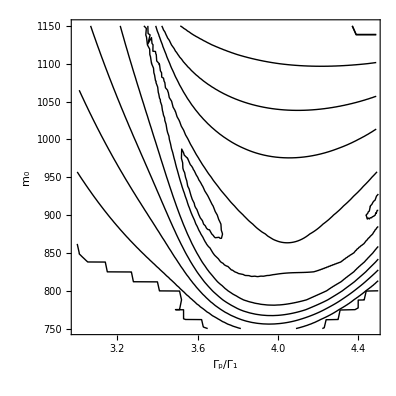

```mathematica
lwPlotChangeM0pv1=  ListContourPlot[ctPlotDataCombppMod,PlotRange->{{3.0,4.48},{750,1150},{-20.6,-14}},Contours->{-20.3,-20,-19,-18,-17,-16,-15,-14}
,ColorFunction->(ColorData["DarkRainbow"][Rescale[#,{-20.6,-14.5}]]&),ColorFunctionScaling->False
,Frame->True
,ContourShading->None
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_p/Γ_1","m_0"}
,ImageSize->5.5 72
(*,AspectRatio->1/GoldenRatio*)
,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log(D)",Black,16,FontFamily->"Cambria"],LabelStyle->Directive[Black,16,FontFamily->"Cambria"]],Right]
,ContourStyle->Directive[Black,Opacity[1]]
(*,ContourLabels->Function[{x,y,z},Text[Framed[Style[z,14,FontFamily->"Cambria"]],{x,y},Background->White]]*)
]
```

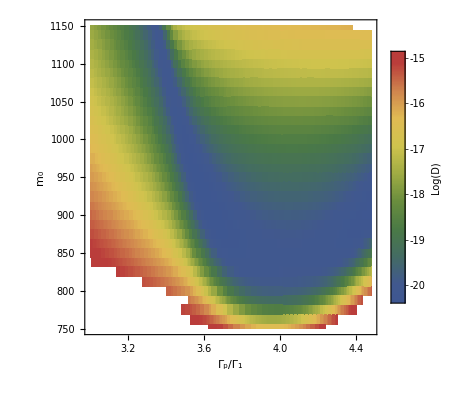

```mathematica
lwPlotChangeM0Densityv1= ListDensityPlot[ctPlotDataCombppMod,PlotRange->{{3.0,4.48},{750,1150},{-20.6,-14}}
,ColorFunction->(ColorData["DarkRainbow"][Rescale[#,{-20.6,-14.5}]]&),ColorFunctionScaling->False
,Frame->True
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_p/Γ_1","m_0"}
,ImageSize->5.5 72
(*,AspectRatio->1/GoldenRatio*)
,InterpolationOrder->0
,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log(D)",Black,16,FontFamily->"Cambria"],LabelStyle->Directive[Black,16,FontFamily->"Cambria"]],Right]]
```

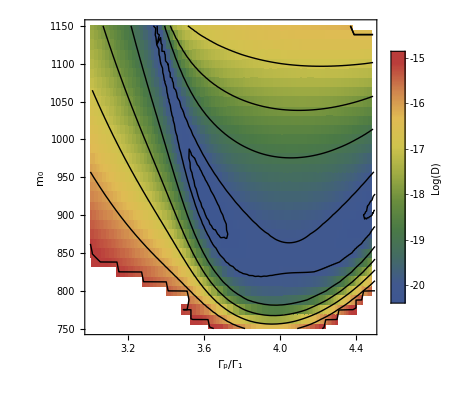

```mathematica
combPlotv1 = Show[lwPlotChangeM0Densityv1,lwPlotChangeM0pv1]
```

```mathematica
bestLWpt=SortBy[ctPlotDataCombppMod,#[[-1]]&][[1]]
```

{3.6,925,-20.4082}

```mathematica
diag =Chop[Diagonal[partialTraceAtom[ FixGSweep2[[-4,2,Position[FixGSweep2[[-4,2,All,1]],bestLWpt[[1]]][[1,1]],2,-1]]]]];
```

```mathematica
Get[ FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[925]<>".m"}]];
Get[FileNameJoin[{bopDir,"new_Bops_m0_"<>ToString[925]<>"_loss.m"}]];
```

```mathematica
tempfun4pp[lambda_?NumericQ,g_?NumericQ]:=Module[{γ,superOp,ev,es,steady,rate,nAvg,state,i,lw},γ=1.;superOp=lambda pumpSO+γ lossSO+g HacSO;{ev,es}=Eigensystem[superOp,-5];steady=SparseArray[Chop[Partition[projector.es⟦-1⟧,Length[aOp]]]];steady=steady/Tr[steady];rate=Tr[AOpc.steady.AOpcD];nAvg=Tr[Transpose[aOp].aOp.steady];lw=9999;For[i=4,i≥1,i=i-1,state=SparseArray[Chop[Partition[projector.es⟦i⟧,Length[aOp]]]];If[Total[Abs[Diagonal[state]]]<1.*^-8,lw=ev⟦i⟧;Break[];]];Return[{nAvg,rate,Log[Abs[lw]],5-i,steady,state}]]
```

```mathematica
ctPlotData4ppp = Table[
temp= FixGSweep4[[j,2]];
temp1 = Select[temp,#[[1]]>4.0&];
temp1 = SortBy[temp1,#[[1]]&];
temp2 = Select[temp,#[[1]]≤4.0&];
temp2 = Reverse[SortBy[temp2,#[[1]]&]];

list1 = {};
For[k=1,k≤Length[temp1],k=k+1,
If[temp1[[k,2,4]]==1,
AppendTo[list1,{temp1[[k,1]],m0List3[[j]],Log[Abs[Exp[temp1[[k,2,3]]]/(temp1[[k,2,2]]/(4 temp1[[k,2,1]]^2))]]}],
Break[]
]
];
While[k≤Length[temp1],
AppendTo[list1,{temp1[[k,1]],m0List3[[j]],Log[9999]}];
k=k+1
];

For[k=1,k≤Length[temp2],k=k+1,
If[temp2[[k,2,4]]==1,
AppendTo[list1,{temp2[[k,1]],m0List3[[j]],Log[Abs[Exp[temp2[[k,2,3]]]/(temp2[[k,2,2]]/(4 temp2[[k,2,1]]^2))]]}],
Break[]
]
];
While[k≤Length[temp2],
AppendTo[list1,{temp2[[k,1]],m0List3[[j]],Log[9999]}];
k=k+1
];

list1
,{j,Length[m0List3]}];
```

```mathematica
ctPlotDataCombppp = Join[Flatten[ctPlotData2ppp,1],Flatten[ctPlotData3ppp,1],Flatten[ctPlotData4ppp,1]];
```

```mathematica
ctPlotDataCombpppMod = {}
Do[
If[ctPlotDataCombppp[[j,1]]==3.11&&ctPlotDataCombppp[[j,2]]==900,
Continue[],
AppendTo[ctPlotDataCombpppMod,ctPlotDataCombppp[[j]]]
]
,{j,Length[ctPlotDataCombppp]}];
```

{}

```mathematica
bestRatioPt=SortBy[ctPlotDataCombpppMod,#[[-1]]&][[1]]
```

{3.59,925,-5.01948}

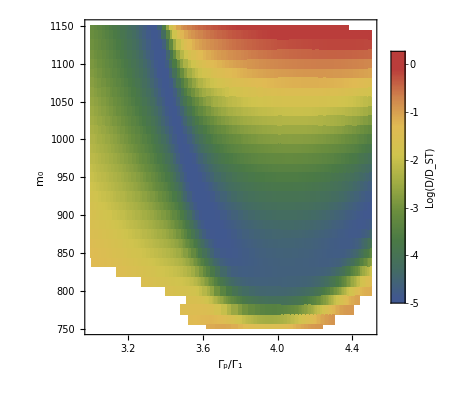

```mathematica
ratioPlt =  ListDensityPlot[ctPlotDataCombpppMod(*,PlotRange->{{3.0,4.48},{750,1000},{-20.6,-14}}*)
,ColorFunction->(ColorData["DarkRainbow"][Rescale[#,{-5.5,0.5}]]&),ColorFunctionScaling->False
,Frame->True
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_p/Γ_1","m_0"}
,ImageSize->5.5 72
(*,AspectRatio->1/GoldenRatio*)
,InterpolationOrder->0
,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log(D/D_ST)",Black,16,FontFamily->"Cambria"],LabelStyle->Directive[Black,16,FontFamily->"Cambria"]],Right]]
```

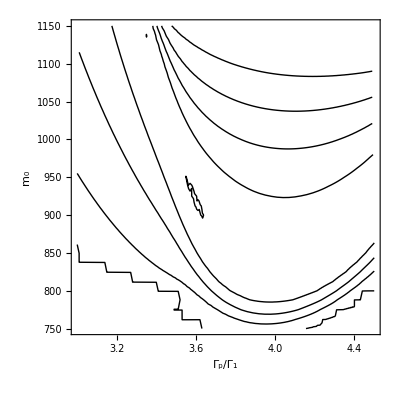

```mathematica
ratioPltCt=  ListContourPlot[ctPlotDataCombpppMod(*,PlotRange->{{3.0,4.48},{750,1150},{-20.6,-14}}*)
,Contours->{-5,-4,-3,-2,-1}
,ColorFunction->(ColorData["DarkRainbow"][Rescale[#,{-20.6,-14.5}]]&),ColorFunctionScaling->False
,Frame->True
,ContourShading->None
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_p/Γ_1","m_0"}
,ImageSize->5.5 72
(*,AspectRatio->1/GoldenRatio*)
,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log(D)",Black,16,FontFamily->"Cambria"],LabelStyle->Directive[Black,16,FontFamily->"Cambria"]],Right]
,ContourStyle->Directive[Black,Opacity[1]]
(*,ContourLabels->Function[{x,y,z},Text[Framed[Style[z,14,FontFamily->"Cambria"]],{x,y},Background->White]]*)
]
```

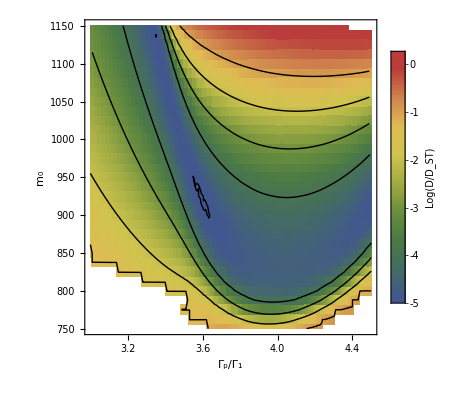

```mathematica
combPlotRatiov1 = Show[ratioPlt,ratioPltCt]
```

## Perturbation on the atom frequency

```mathematica
updateABOCCopsNew[zc1000]
```

```mathematica
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[1000]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];
```

```mathematica
aTrunc = 2500;
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];
```

```mathematica
atomDetune = KroneckerProduct[iaop,SparseArray[sp.sm]];
atomDetuneSO = -ⅈ ( projectorD.combineOps[atomDetune,iOp].projector-projectorD.combineOps[iOp,atomDetune].projector);
```

```mathematica
tempfun4[lambda_?NumericQ,g_?NumericQ,Δ_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO + Δ atomDetuneSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[{nAvg,rate,Log[Abs[ev[[-2]]]],steady}]
]
```

```mathematica
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
res1
```

{-20.2698,{x→3.5,y→1.0013}}

```mathematica
tempfun[3.5,1.0]
```

-20.1609

```mathematica
lambdaBest = x/.res1[[2]]
```

3.5

```mathematica
gBest = y x/2 √(1.0/(x- 2))/.res1[[2]]
```

1.43072

```mathematica
testResult = tempfun4[lambdaBest,gBest,0.];
```

```mathematica
testResult
```

{1079.03+1.70918×10^-8 ⅈ,1.00195+6.36961×10^-13 ⅈ,-20.2698,SparseArray[…]}

```mathematica
testResult1 = tempfun4[lambdaBest,gBest,0.1];
```

```mathematica
testResult1
```

{1240.71-9.86334×10^-9 ⅈ,1.00829+1.36379×10^-13 ⅈ,-13.188,SparseArray[…]}

```mathematica
tempfun4p[lambda_?NumericQ,g_?NumericQ,Δ_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO + Δ atomDetuneSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[Log[Abs[ev[[-2]]/(rate/(4 nAvg^2))]]]
]
```

```mathematica
tempfun4pp[lambda_?NumericQ,g_?NumericQ,Δ_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO + Δ atomDetuneSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];


Return[Abs[ev[[-2]]]]
]
```

```mathematica
tempRes =Quiet[ FindMinimum[ tempfun4p[x,y,0.],{x,lambdaBest,0.8 lambdaBest,1.5 lambdaBest},{y,gBest,0.8 gBest, 1.2 gBest}]]
```

{-4.94781,{x→3.49993,y→1.42974}}

```mathematica
cordList = 10^Range[-4,-1,0.1]
```

{0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1}

```mathematica
mesh = Table[
{x lambdaBest,y gBest} 
,{x,0.95,2.0,0.05}
,{y,0.9,1.21,0.02} ];
mesh = Flatten[mesh,1];
mesh//Dimensions
```

{352,2}

```mathematica
optimizeLPara[g_?NumericQ,δ_?NumericQ,lambda1_?NumericQ,lambda2_?NumericQ,round_?IntegerQ]:=Module[{lineTemp,n,lambdaInitial,lambdaFinal,step,tempCoord,tempRes,minLW},
n = Length[Kernels[]];

If[n≤2, Print["Kernels are not enough"];Return[]];

lambdaInitial = lambda1;
lambdaFinal= lambda2;


Do[
step = 1.(lambdaFinal-lambdaInitial)/(n-1);
tempCoord = Range[lambdaInitial,lambdaFinal,step];

tempRes = ParallelTable[
{tempCoord[[j]],tempfun4pp[tempCoord[[j]],g,δ]}
,{j,Length[tempCoord]}];

minLW = SortBy[tempRes,#[[2]]&][[1]];

lambdaInitial = minLW[[1]]-step/2;
lambdaFinal = minLW[[1]]+step/2;
,{rd, round}];

Return[minLW]
]
```

```mathematica
Monitor[
linewidthPos= Table[
res = FindMinimum[ tempfun4pp[x,y,cordList[[j]]],{x,lambdaBest,0.8 lambdaBest,1.5 lambdaBest},{y,gBest,0.8 gBest, 1.2 gBest},PrecisionGoal->1,AccuracyGoal->1];

{cordList[[j]],res[[1]],x/.res[[2]],y/.res[[2]]}
,{j,Length[cordList]}
];
,j]
```

```mathematica
x=.
```

```mathematica
y=.
```

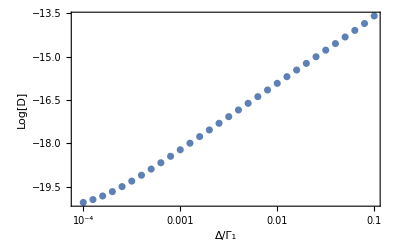

```mathematica
ListLogLinearPlot[{#[[1]],Log[Abs[#[[2]]]]}&/@linewidthPos
,PlotRange->Full
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Δ/Γ_1","Log[D]"}
,ImageSize->5.5 72
,FrameTicks->{{Automatic,Automatic},{{{1*^-4,"10^-4"},{.5*^-3," "},{1.*^-3,"10^-3"},{.5*^-2," "},{1.*^-2,"10^-2"},{.5*^-1,""},{0.1,"10^-1"}},Automatic}}]
```

```mathematica
allData=Table[
 tempfun4[linewidthPos[[j,3]],linewidthPos[[j,4]],linewidthPos[[j,1]]]
,{j,Length[linewidthPos]}];
```

```mathematica
bestTemp = FindMinimum[ tempfun4pp[x,y,0.],{x,lambdaBest,0.8 lambdaBest,1.5 lambdaBest},{y,gBest,0.8 gBest, 1.2 gBest},PrecisionGoal->1,AccuracyGoal->1]
```

{1.57374×10^-9,{x→3.5,y→1.43072}}

```mathematica
bestLW = tempfun4[x/.bestTemp[[2]],y/.bestTemp[[2]],0];
bestLWratio = Log[Abs[Exp[bestLW[[3]]]/(bestLW[[2]]/(4 bestLW[[1]]^2))]]
```

-4.91782

```mathematica
reScale[x_]:=(2-(-5))/(1085 -1000)(x-1000)-5
```

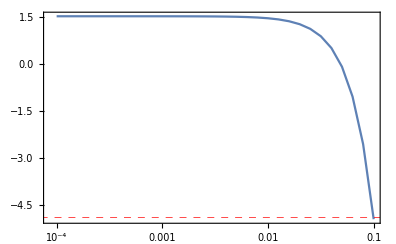

```mathematica
ListLogLinearPlot[Transpose[{linewidthPos[[All,1]],reScale[Abs[allData[[All,1]]]]}]
,PlotRange->Full
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
(*,FrameLabel->{"Δ/Γ_1","Log(D/D_ST)"}*)
,GridLines->{None,{{bestLWratio,Directive[Red,Dashed,Opacity[1]]}}}
,ImageSize->5.5 72
,FrameTicks->{{Automatic,Automatic},{{{1*^-4,"10^-4"},{.5*^-3," "},{1.*^-3,"10^-3"},{.5*^-2," "},{1.*^-2,"10^-2"},{.5*^-1,""},{0.1,"10^-1"}},Automatic}}
,Joined->True
]
```

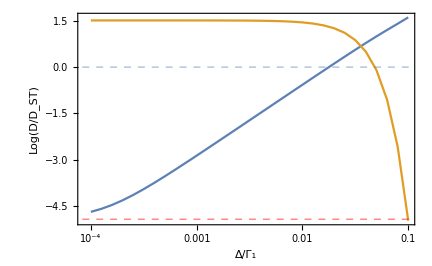

```mathematica
ListLogLinearPlot[
{Transpose[{linewidthPos[[All,1]],Log[Abs[Exp[allData[[All,3]]]/(allData[[All,2]]/(4 allData[[All,1]]^2))]]}]
,Transpose[{linewidthPos[[All,1]],reScale[Abs[allData[[All,1]]]]}]}
,PlotRange->Full
,Frame->True
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Cambria"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Cambria"]},{Directive[Black,FontSize->16,FontFamily->"Cambria"]
,Directive[Black,FontSize->16,FontFamily->"Cambria"]}
}
,FrameLabel->{{"Log(D/D_ST)",Rotate["⟨n⟩",π]},{"Δ/Γ_1",None}}
,GridLines->{None,{{0,Directive[ColorData[97][1],Dashed,Opacity[1]]},{bestLWratio,Directive[Red,Dashed,Opacity[1]]}}}
,ImageSize->6.0 72
,Axes->None
,FrameTicks->{{Automatic,{{reScale[1080],1080},{reScale[1060],1060},{reScale[1040],1040},{reScale[1020],1020},{reScale[1000],1000}}},{{{1*^-4,"10^-4"},{.5*^-3," "},{1.*^-3,"10^-3"},{.5*^-2," "},{1.*^-2,"10^-2"},{.5*^-1,""},{0.1,"10^-1"}},Automatic}}
,Joined->True
,PlotStyle->{{ColorData[97][1]},{ColorData[97][2]}}
]
```